```mathematica
For[run=1,run<4,run++,
skip=20;
du=dv=1/100;
massReduct=1/1000;
v1= 0;
m0=1;
Q0=8/10;
SourcesRParam =1;
SourcesRParamR ={1,-1,1}[[run]];
SourcesSParam = {1,0,0}[[run]];
SourcesSParamR ={1,1,2}[[run]];
SourcesS5Param =1;
deltaUV5Param = 70;
QuvFactor =1;
Qreduct=Q0/m0*massReduct;
deltav =900;
v2 =v1+deltav;
RStarConst =-30;
Vvec = Table[v,{v,v1,v2,dv}];
MFunc = (m0^3-(v-v1)*massReduct)^(1/3);
QFunc = MFunc * Q0;
Clear[pdesolskip,RTable,STable,RvTable,RvvTable,RuTable,RuuTable,SvTable,SvvTable,SuTable,SuuTable];
Uvec = 2*RStarConst- Vvec;
Uvec0=Table[u,{u,Uvec[[-1]],Uvec[[1]],du}];
UvecSkipped = Uvec0[[1;;-1;;skip]];
VvecSkipped = Vvec[[1;;-1;;skip]];
deltaUV5 = (Uvec0[[1]]+Vvec[[1]])/2+deltaUV5Param; 
vsol=DSolve[{H'[v]==κp/.{Q->QFunc,m->MFunc},H[0]==0},H[v],{v,v1,v2}(*,Method->"StiffnessSwitching",WorkingPrecision->60*)];
vtilde=(H[v]/.vsol/.{v->Vvec})[[1]];
usol=DSolve[{H'[u]==κp/.{Q->(QFunc/.v->-u),m->(MFunc/.v->-u)},H[0]==0},H[u],u(*,{u,Uvec[[1]],Uvec[[-1]]},Method->"StiffnessSwitching",WorkingPrecision->60*)];
utilde=(H[u]/.usol/.{u->Uvec})[[1]];
Ttilde=(utilde+vtilde)/2;
MTable= MFunc/.{v->Vvec}//N100;
QTable = QFunc/.{v->Vvec}//N100;
QuvTable = QuvFactor *massReduct* MTable^-1 ;
QuvScale=MTable^-1;
MuTable = MFunc /. {v->-Uvec}//N100;
QuTable = QFunc /. {v->-Uvec}//N100;
κpu=(κp/.{m->μ,Q->Qu});
sInitFixed = Log[-r *f/2]+Log[κpu]-Log[κp];
DRDUFixed=r f *κpu/κp;
DLogκpuDu=D[Log[κpu],μ]*D[(MFunc/.v->-u),u]+D[Log[κpu],Qu]*D[(QFunc/.v->-u),u];
DSDUFixed=D[Log[-r f ],r] *DRDUFixed/(2r)+DLogκpuDu;
SourcesR=massReduct*SourcesRParam/MTable^3;
SourcesS = massReduct*SourcesSParam/MTable^5;
SourcesRR =massReduct* SourcesRParamR/MTable^4;
SourcesRS = massReduct*SourcesSParamR/MTable^6;
SourcesR5=0*Vvec;
SourcesS5 = massReduct*SourcesS5Param*MTable;
time0=AbsoluteTiming[
RStarVector=Table[ (Ttilde[[j]]/κp/.{m->MTable[[j]],Q->QTable[[j]]}),{j,1,Length[MTable]}];
rInit=Table[RFromRStar[RStarVector[[j]],MTable[[j]],QTable[[j]]],{j,1,Length[MTable]}];
RInitVector = Table[ rInit[[j]]^2,{j,1,Length[MTable]}];
SInitVector =  Table[ (sInitFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DRInitVector =  Table[ (DRDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DSInitVector =  Table[ (DSDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],u->Uvec[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
midpointDR = (DRInitVector[[2;;]]+DRInitVector[[;;-2]])/2;
midpointDS = (DSInitVector[[2;;]]+DSInitVector[[;;-2]])/2;
{Ruv,Suv}=ComputeRuvSuvQuvScale[RInitVector,SInitVector,(QTable[[2;;]]+QTable[[;;-2]])/2,SourcesR,SourcesS,QuvTable,Uvec0[[1]]+Vvec[[1]],QuvScale, dv,SourcesRR,SourcesRS,SourcesR5,SourcesS5,deltaUV5];
R2InitVector=RInitVector[[2;;]]+du*(midpointDR+1/2*dv*Ruv);
S2InitVector=SInitVector[[2;;]]+du*(midpointDS+1/2*dv*Suv);];
time2=AbsoluteTiming[pdesolskip=pyPdeSolveQuvScale[skip,R2InitVector,RInitVector,S2InitVector,SInitVector,(QTable//N),(du//N),(dv//N),SourcesR//N,SourcesS//N,QuvTable//N,(Uvec0[[1]]+Vvec[[1]])//N, QuvScale // N,SourcesRR//N,SourcesRS//N,SourcesR5 // N,SourcesS5//N,deltaUV5//N];];
(* R,S,Rv,Rvv,Ru,Ruu,Sv,Svv,Su,Suu *)
RTable = Normal[pdesolskip[[1]]];
STable = Normal[pdesolskip[[2]]];
RvTable = Normal[pdesolskip[[3]]];
RvvTable = Normal[pdesolskip[[4]]];
RuTable = Normal[pdesolskip[[5]]];
RuuTable = Normal[pdesolskip[[6]]];
SvTable = Normal[pdesolskip[[7]]];
SvvTable = Normal[pdesolskip[[8]]];
SuTable = Normal[pdesolskip[[9]]];
SuuTable = Normal[pdesolskip[[10]]];
cu = RuTable*SuTable-RuuTable;
cv = RvTable*SvTable-RvvTable;
cuv = cu-cv;
RTables[run] = RTable;
STables[run] = STable;
RvTables[run] = RvTable;
RvvTables[run] = RvvTable;
RuTables[run] = RuTable;
RuuTables[run] = RuuTable;
SvTables[run] = SvTable;
SvvTables[run] = SvvTable;
SuTables[run] = SuTable;
SuuTables[run] = SuuTable;
cus[run]=cu;
cvs[run]=cv;
]
```

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

```mathematica
ThePlotLegend=MaTeX/@{"run\;1","run\;2","run\;3"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
TheImageSize=250
```

250

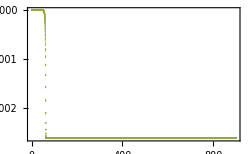

```mathematica
ExportAndShow["Tuu(v)",ListPlot[Table[{VvecSkipped[[3;;]],cus[run][[3;;,-2]]}//Transpose,{run,1,3}],Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]},PlotRange->All,PlotLegends->ThePlotLegend,ImageSize->TheImageSize]]
```

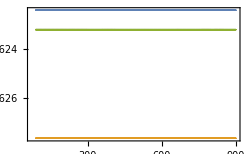

```mathematica
ExportAndShow["Tuu(v) region 3",ListPlot[Table[{VvecSkipped[[450;;]],cus[run][[450;;,-2]]}//Transpose,{run,1,3}],Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]},PlotRange->All,PlotLegends->ThePlotLegend,ImageSize->TheImageSize]]
```

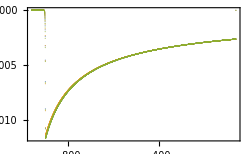

```mathematica
ExportAndShow["Tuu(u)",ListPlot[Table[{UvecSkipped[[3;;]],cus[run][[-2,3;;]]}//Transpose,{run,1,3}],Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]},PlotRange->All,PlotLegends->ThePlotLegend,ImageSize->TheImageSize]]
```

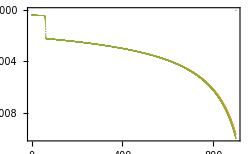

```mathematica
ExportAndShow["Tvv(v)",ListPlot[Table[{VvecSkipped[[3;;]],cvs[run][[3;;,-2]]}//Transpose,{run,1,3}],Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]},PlotRange->All,PlotLegends->ThePlotLegend,ImageSize->TheImageSize]]
```

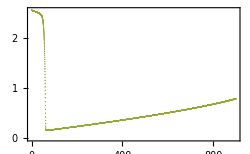

```mathematica
ExportAndShow["R(v)",ListPlot[Table[{VvecSkipped[[3;;]],RTables[run][[3;;,-2]]}//Transpose,{run,1,3}],Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R",-90 Degree]},PlotRange->All,PlotLegends->ThePlotLegend,ImageSize->TheImageSize]]
```

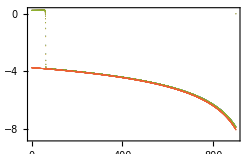

```mathematica
ExportAndShow["S,v",ListPlot[Join[Table[{VvecSkipped,SvTables[run][[;;,-1]]}//Transpose,{run,1,3}],{{VvecSkipped,-κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}}//Transpose}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S_{,v}\\;run1","S_{,v}\\;run2","S_{,v}\\;run3","-\\kappa_-^v"},ImageSize->TheImageSize]]
```

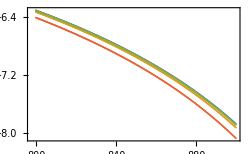

```mathematica
ExportAndShow["S,v zoomed",ListPlot[Join[Table[({VvecSkipped,SvTables[run][[;;,-1]]}//Transpose)[[4000;;-2]],{run,1,3}],{({VvecSkipped,-κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}}//Transpose)[[4000;;-2]]}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S_{,v}\\;run1","S_{,v}\\;run2","S_{,v}\\;run3","-\\kappa_-^v"},ImageSize->TheImageSize]]
```

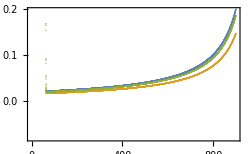

```mathematica
κmVec=-κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]};
ExportAndShow["S,v+κ-",ListPlot[Table[{VvecSkipped,SvTables[run][[;;,-1]]-κmVec}//Transpose,{run,1,3}],Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"S_{,v}+\\kappa_-^v",-90 Degree]},PlotLegends->ThePlotLegend,ImageSize->TheImageSize]]
```

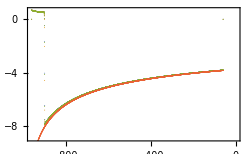

```mathematica
ExportAndShow["S,u",ListPlot[Join[Table[{UvecSkipped,SuTables[run][[-1,;;]]}//Transpose,{run,1,3}],{{UvecSkipped,-κm/.{m->MFunc/.{v->-UvecSkipped},Q->QFunc/.{v->-UvecSkipped}}}//Transpose}],Frame->True,FrameLabel->{MaTeX@"u"},PlotLegends->MaTeX/@{"S_{,u}\\;run1","S_{,u}\\;run2","S_{,u}\\;run3","-\\kappa_-^u"},ImageSize->TheImageSize]]
```

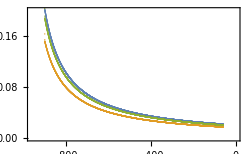

```mathematica
κmUVec=-κm/.{m->MFunc/.{v->-UvecSkipped},Q->QFunc/.{v->-UvecSkipped}};
ExportAndShow["S,u+κ-",ListPlot[Table[{UvecSkipped,SuTables[run][[-1,;;]]-κmUVec}//Transpose,{run,1,3}],Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"S_{,u}+\\kappa_-^u",-90 Degree]},PlotLegends->ThePlotLegend,ImageSize->TheImageSize]]
```

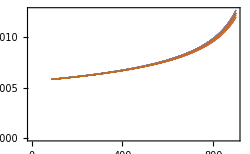

```mathematica
ExportAndShow["R,v",ListPlot[Flatten[Table[{{VvecSkipped[[450;;-2]],RvTables[run][[450;;-2,-1]]}//Transpose,{VvecSkipped[[450;;-2]],(-cvs[run][[;;,-1]]/(κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}))[[450;;-2]]}//Transpose},{run,1,3}],1],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"R_{,v}\\;run1","-\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}\\;run1","R_{,v}\\;run2","-\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}\\;run2","R_{,v}\\;run3","-\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}\\;run3"},ImageSize->TheImageSize]]
```

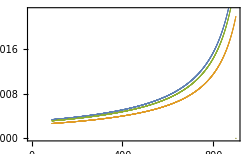

```mathematica
ExportAndShow["R,v-approx",ListPlot[Table[{VvecSkipped[[450;;]],RvTables[run][[450;;,-1]]-(-cvs[run][[;;,-1]]/(κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}))[[450;;]]}//Transpose,{run,1,3}],Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R_{,v}+\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}",-90 Degree]},PlotLegends->MaTeX/@{"run1","run2","run3"},ImageSize->TheImageSize]]
```

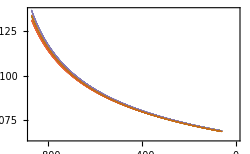

```mathematica
κmUVec=-κm/.{m->MFunc/.{v->-UvecSkipped},Q->QFunc/.{v->-UvecSkipped}};
ExportAndShow["R,u",ListPlot[Flatten[Table[{{UvecSkipped[[450;;-2]],RuTables[run][[-2,450;;-2]]}//Transpose,{UvecSkipped[[450;;-2]],(cus[run][[-2,;;]]/κmUVec)[[450;;-2]]}//Transpose},{run,1,3}],1],Frame->True,FrameLabel->{MaTeX@"u"},PlotLegends->MaTeX/@{"R_{,u}\\;run1","-\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}\\;run1","R_{,u}\\;run2","-\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}\\;run2","R_{,u}\\;run3","-\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}\\;run3"},ImageSize->TheImageSize]]
```

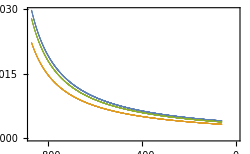

```mathematica
κmUVec=-κm/.{m->MFunc/.{v->-UvecSkipped},Q->QFunc/.{v->-UvecSkipped}};
ExportAndShow["R,u-approx",ListPlot[Flatten[Table[{{UvecSkipped[[450;;-2]],RuTables[run][[-2,450;;-2]]-(cus[run][[-2,;;]]/κmUVec)[[450;;-2]]}//Transpose},{run,1,3}],1],Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"R_{,u}+\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}",-90 Degree]},PlotLegends->MaTeX/@{"run1","run2","run3"},ImageSize->TheImageSize]]
```